```mathematica
SetDirectory@NotebookDirectory[];
Import["Qubits_package.m"];
Import["ExactKrylov_package.m"];
```

## Parameters

```mathematica
Nq=10;
HamType="Heisenberg";
(*HamType="FermiHubbard";*)
GraphType="Chain";
(*GraphType="Ladder";*)
(*GraphType=ToString[2];*)
```

```mathematica
d=5;
logηList=Table[-0.1*j,{j,-50,150}];
Ide=IdentityMatrix[d];
PR={{1.*^-3,1.*^12},{1.*^-14,1.*^1}};
```

```mathematica
seed=RandomInteger[{1,1000000}]; 
seed=123; 
SeedRandom[seed];
```

## Model

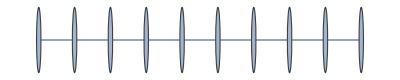

```mathematica
If[StringMatchQ[HamType,"Heisenberg"],(
EL=funGraph[Nq,GraphType];
Model=funHeisenberg[Nq,EL]
)];
If[StringMatchQ[HamType,"FermiHubbard"],(
EL=funGraph[Nq/2,GraphType];
u=1.;
Model=funFermiHubbard[Nq,EL,u]
)];
Graph[EL]
```

```mathematica
Ham=funHamiltonianQubit[Model];
```

## Spectrum

```mathematica
{EE,ES}=funSpectrum[Ham];
HamNorm=Max[Abs[EE]];
EE=EE/HamNorm;
Eg=EE[[1]]
```

-1.

```mathematica
If[StringMatchQ[HamType,"Heisenberg"],(
htot=3.*Length[EL]/HamNorm
)]
If[StringMatchQ[HamType,"FermiHubbard"],(
htot=(2.*Length[EL]+u/4.*Nq/2.)/HamNorm
)]
```

1.58524

## Reference state

```mathematica
If[StringMatchQ[HamType,"Heisenberg"],(
ψ=funPairwiseSinglet[Nq]
)];
If[StringMatchQ[HamType,"FermiHubbard"],(
ψ=funHartreeFock[Nq,EL]
)];
ψ=Conjugate[ES].ψ;
ψ=Flatten[ψ];
Proψ=Abs[ψ]^2;
```

```mathematica
pg=Proψ[[1]]
ER=Total[Proψ*EE];
ϵR=ER-Eg
```

0.682614

0.119312

## Power

```mathematica
E0=Eg+1.;
{Hmat,Smat}=funMatPower[EE,Proψ,d,E0];
```

```mathematica
EB=Hmat[[d,d]]/Smat[[d,d]];
ϵB=EB-Eg
```

0.0072981

```mathematica
logη=-15;
η=10.^logη;
{EK,cn}=funDiagonalisation[Hmat+2.*η*Ide,Smat+2.*η*Ide];
ϵK=EK-Eg
```

0.000390209

```mathematica
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
```

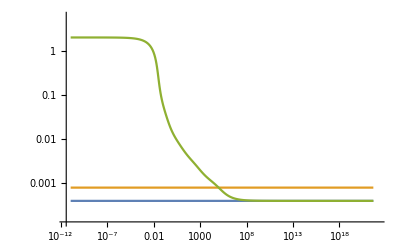

```mathematica
ListLogLogPlot[{Transpose[{γList,0.*ϵList+ϵK}],Transpose[{γList,0.*ϵList+2.*ϵK}],Transpose[{γList,ϵList}]},PlotRange->{{Min[γList]/3,Max[γList]*3},{Min[Join[ϵList,{ϵR,ϵK}]]/3,Max[Join[ϵList,{ϵR,ϵK}]]*3}},Joined->True]
```

```mathematica
γListP=γList;
ϵListP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)]
γP=γ
```

96610.8

## Chebyshev polynomial

```mathematica
E0=0;
{Hmat,Smat}=funMatChebyshev[EE,Proψ,d,htot,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
```

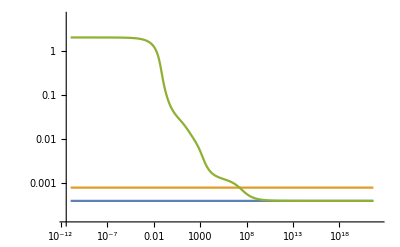

```mathematica
ListLogLogPlot[{Transpose[{γList,0.*ϵList+ϵK}],Transpose[{γList,0.*ϵList+2.*ϵK}],Transpose[{γList,ϵList}]},PlotRange->{{Min[γList]/3,Max[γList]*3},{Min[Join[ϵList,{ϵR,ϵK}]]/3,Max[Join[ϵList,{ϵR,ϵK}]]*3}},Joined->True]
```

```mathematica
γListCP=γList;
ϵListCP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)]
γCP=γ
```

1.71996×10^7

## Gaussian-Power

```mathematica
E0=Eg;
τMIN=0;
τMAX=64;
Do[(
τ=(τMIN+τMAX)/2.;

{Hmat,Smat}=funMatGaussianPower[EE,Proψ,1,htot,τ,E0];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;

If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
(*Print[{err,τMIN,τMAX,ToString[Now]}];*)
),{j,1,30}];
τ=(τMIN+τMAX)/2.
```

6.34638

```mathematica
E0=Eg;
{Hmat,Smat}=funMatGaussianPower[EE,Proψ,d,htot,τ,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,htot,1.,logηList];
```

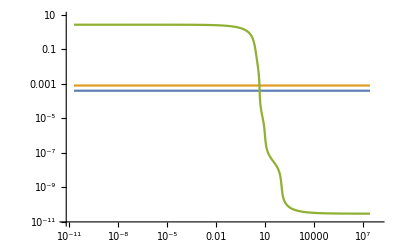

```mathematica
ListLogLogPlot[{Transpose[{γList,0.*ϵList+ϵK}],Transpose[{γList,0.*ϵList+2.*ϵK}],Transpose[{γList,ϵList}]},PlotRange->{{Min[γList]/3,Max[γList]*3},{Min[Join[ϵList,{ϵR,ϵK}]]/3,Max[Join[ϵList,{ϵR,ϵK}]]*3}},Joined->True]
```

```mathematica
γListGP=γList;
ϵListGP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)]
γGP=γ
```

4.41987

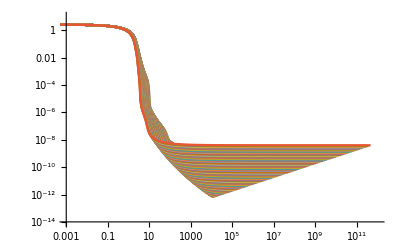

```mathematica
δList=Table[0.002*j,{j,-50,50}];
δCurves={};
Do[(
δ=δList[[j]];

E0=Eg+δ;
{Hmat,Smat}=funMatGaussianPower[EE,Proψ,d,htot,τ,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,htot,1.,logηList];

AppendTo[δCurves,Transpose[{γList,ϵList}]]
),{j,1,Length[δList]}]
ListLogLogPlot[δCurves,PlotRange->PR,Joined->True]
```

## Inverse Power

```mathematica
E0=Eg-1.;
{Hmat,Smat}=funMatInversePower[EE,Proψ,d,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
```

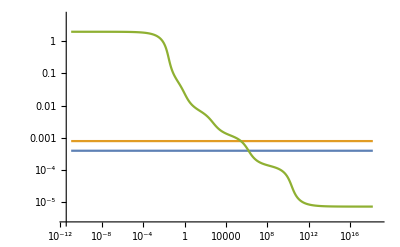

```mathematica
ListLogLogPlot[{Transpose[{γList,0.*ϵList+ϵK}],Transpose[{γList,0.*ϵList+2.*ϵK}],Transpose[{γList,ϵList}]},PlotRange->{{Min[γList]/3,Max[γList]*3},{Min[Join[ϵList,{ϵR,ϵK}]]/3,Max[Join[ϵList,{ϵR,ϵK}]]*3}},Joined->True]
```

```mathematica
γListIP=γList;
ϵListIP=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)]
γIP=γ
```

276085.

## Imaginary-time evolution

```mathematica
E0=Eg;
τMIN=0;
τMAX=64;
Do[(
τ=(τMIN+τMAX)/2.;

{Hmat,Smat}=funMatITE[EE,Proψ,d,τ,E0];
EK=Hmat[[d,d]]/Smat[[d,d]];
err=EK-Eg;

If[err>ϵB,τMIN=τ];
If[err<ϵB,τMAX=τ];
(*Print[{err,τMIN,τMAX,ToString[Now]}];*)
),{j,1,30}];
τ=(τMIN+τMAX)/2.
```

1.1768

```mathematica
E0=Eg;
{Hmat,Smat}=funMatITE[EE,Proψ,d,τ,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
```

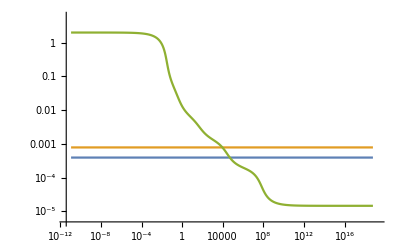

```mathematica
ListLogLogPlot[{Transpose[{γList,0.*ϵList+ϵK}],Transpose[{γList,0.*ϵList+2.*ϵK}],Transpose[{γList,ϵList}]},PlotRange->{{Min[γList]/3,Max[γList]*3},{Min[Join[ϵList,{ϵR,ϵK}]]/3,Max[Join[ϵList,{ϵR,ϵK}]]*3}},Joined->True]
```

```mathematica
γListITE=γList;
ϵListITE=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)]
γITE=γ
```

8964.89

## Real-time evolution

0.314159

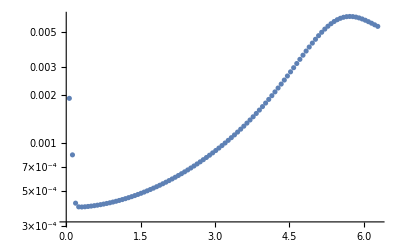

```mathematica
ΔtList=Table[(2.*PI)/100 j,{j,1,100}];
ϵKList=ΔtList;
Do[(
Δt=ΔtList[[j]];

E0=Eg;
{Hmat,Smat}=funMatRTE[EE,Proψ,d,Δt,E0];
logη=-15;
η=10.^logη;
{EK,cn}=funDiagonalisation[Hmat+2.*η*Ide,Smat+2.*η*Ide];
err=EK-Eg;

ϵKList[[j]]=err
),{j,1,Length[ΔtList]}]
Δt=ΔtList[[Position[ϵKList,Min[ϵKList]][[1,1]]]]
ListLogPlot[Transpose[{ΔtList,ϵKList}],PlotRange->Full]
```

```mathematica
E0=Eg;
{Hmat,Smat}=funMatRTE[EE,Proψ,d,Δt,E0];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
```

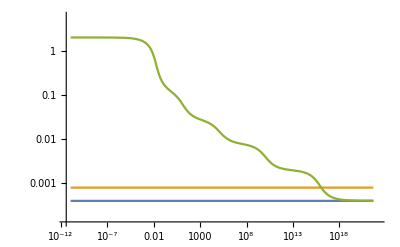

```mathematica
ListLogLogPlot[{Transpose[{γList,0.*ϵList+ϵK}],Transpose[{γList,0.*ϵList+2.*ϵK}],Transpose[{γList,ϵList}]},PlotRange->{{Min[γList]/3,Max[γList]*3},{Min[Join[ϵList,{ϵR,ϵK}]]/3,Max[Join[ϵList,{ϵR,ϵK}]]*3}},Joined->True]
```

```mathematica
γListRTE=γList;
ϵListRTE=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)]
γRTE=γ
```

1.11593×10^16

## Filter

```mathematica
ΔE=0.;
E0=Eg;
τMIN=0;
τMAX=64;
Do[(
T=(τMIN+τMAX)/2.;

{Hmat,Smat}=funMatFilter[EE,Proψ,d,T,E0,ΔE];
EK=Hmat[[1,1]]/Smat[[1,1]];
err=EK-Eg;

If[err>ϵB,τMIN=T];
If[err<ϵB,τMAX=T];
(*Print[{err,τMIN,τMAX,ToString[Now]}];*)
),{j,1,30}];
T=(τMIN+τMAX)/2.
```

11.2447

0.02

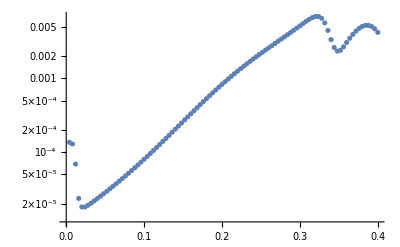

```mathematica
ΔEList=Table[2./(d*100)*j,{j,1,100}];
ϵKList=ΔEList;
Do[(
ΔE=ΔEList[[j]];

E0=Eg;
{Hmat,Smat}=funMatFilter[EE,Proψ,d,T,E0,ΔE];
logη=-15;
η=10.^logη;
{EK,cn}=funDiagonalisation[Hmat+2.*η*Ide,Smat+2.*η*Ide];
err=EK-Eg;

ϵKList[[j]]=err;
),{j,1,Length[ΔEList]}]
ΔE=ΔEList[[Position[ϵKList,Min[ϵKList]][[1,1]]]]
ListLogPlot[Transpose[{ΔEList,ϵKList}],PlotRange->Full]
```

```mathematica
E0=Eg;
{Hmat,Smat}=funMatFilter[EE,Proψ,d,T,E0,ΔE];
{γList,ϵList}=funGammaEpsilon[Eg,pg,Hmat,Smat,Ide,1.,1.,logηList];
```

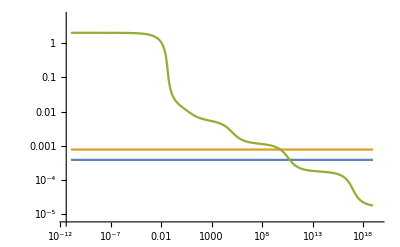

```mathematica
ListLogLogPlot[{Transpose[{γList,0.*ϵList+ϵK}],Transpose[{γList,0.*ϵList+2.*ϵK}],Transpose[{γList,ϵList}]},PlotRange->{{Min[γList]/3,Max[γList]*3},{Min[Join[ϵList,{ϵR,ϵK}]]/3,Max[Join[ϵList,{ϵR,ϵK}]]*3}},Joined->True]
```

```mathematica
γListF=γList;
ϵListF=ϵList;
ϵMin=Min[ϵList];
If[ϵMin<2.*ϵK,(
γ=funInterpolation[ϵList,γList,2.*ϵK];
),(
γ=0.;
)]
γF=γ
```

6.4194×10^9

## Plot

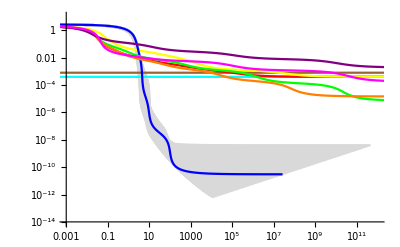

```mathematica
ListLogLogPlot[Join[δCurves,{Transpose[{γListP,0.*ϵListP+ϵK}],Transpose[{γListP,0.*ϵListP+2.*ϵK}],Transpose[{γListP,ϵListP}],Transpose[{γListCP,ϵListCP}],Transpose[{γListGP,ϵListGP}],Transpose[{γListIP,ϵListIP}],Transpose[{γListITE,ϵListITE}],Transpose[{γListRTE,ϵListRTE}],Transpose[{γListF,ϵListF}]}],PlotRange->PR,Joined->True,PlotStyle->Join[Table[LightGray,Length[δCurves]],{Cyan,Brown,Red,Yellow,Blue,Green,Orange,Purple,Magenta}]]
```

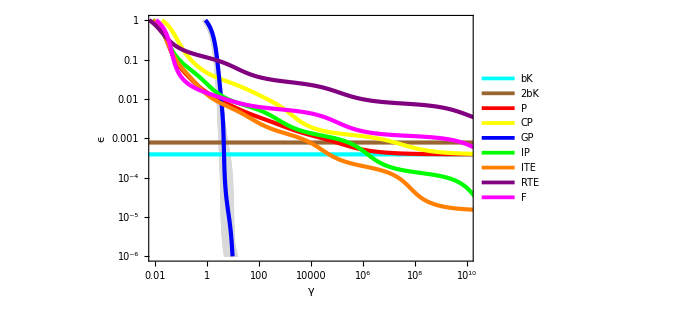

```mathematica
PR={{1.*^-2,1.*^10},{1.*^-6,1.*^0}};
plot1=ListLogLogPlot[δCurves,PlotRange->PR,Joined->True,PlotStyle->Table[LightGray,Length[δCurves]],Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"γ","ϵ"}];
plot2=ListLogLogPlot[{Transpose[{γListP,0.*ϵListP+ϵK}],Transpose[{γListP,0.*ϵListP+2.*ϵK}],Transpose[{γListP,ϵListP}],Transpose[{γListCP,ϵListCP}],Transpose[{γListGP,ϵListGP}],Transpose[{γListIP,ϵListIP}],Transpose[{γListITE,ϵListITE}],Transpose[{γListRTE,ϵListRTE}],Transpose[{γListF,ϵListF}]},PlotRange->PR,Joined->True,PlotStyle->{{Thickness[0.006],Cyan},{Thickness[0.006],Brown},{Thickness[0.006],Red},{Thickness[0.006],Yellow},{Thickness[0.006],Blue},{Thickness[0.006],Green},{Thickness[0.006],Orange},{Thickness[0.006],Purple},{Thickness[0.006],Magenta}},Frame->True,FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive[Black,Thickness[0.002]],FrameLabel->{"γ","ϵ"},PlotLegends->Placed[LineLegend[{"bK","2bK","P","CP","GP","IP","ITE","RTE","F"},LegendFunction->(Framed[#,FrameStyle->LightGray]&),LegendMarkerSize->{16,8},LabelStyle->{Black,Bold,FontSize->12,FontFamily->"Arial"},LegendMargins->0,LegendLayout->{"Column",3}],{0.79,0.84}]];
Show[plot1,plot2,LabelStyle->{FontSize->18,FontFamily->"Arial"},ImageSize->500]
```

## Data

```mathematica
If[!StringMatchQ[GraphType, "Chain"]&&!StringMatchQ[GraphType, "Ladder"], GraphType="Random"];
```

```mathematica
path=ToString[HamType]<>"-"<>ToString[GraphType]<>"-Nq="<>ToString[Nq]<>"-d="<>ToString[d]<>".dat";
CreateFile[path];
file=File[path];
```

```mathematica
Data={};
AppendTo[Data,"ϵR:"];
AppendTo[Data,ϵR];
AppendTo[Data,""];
AppendTo[Data,"ϵB:"];
AppendTo[Data,ϵB];
AppendTo[Data,""];
AppendTo[Data,"ϵK:"];
AppendTo[Data,ϵK];
AppendTo[Data,""];
AppendTo[Data,"γP:"];
AppendTo[Data,γP];
AppendTo[Data,""];
AppendTo[Data,"γCP:"];
AppendTo[Data,γCP];
AppendTo[Data,""];
AppendTo[Data,"γGP:"];
AppendTo[Data,γGP];
AppendTo[Data,""];
AppendTo[Data,"γIP:"];
AppendTo[Data,γIP];
AppendTo[Data,""];
AppendTo[Data,"γITE:"];
AppendTo[Data,γITE];
AppendTo[Data,""];
AppendTo[Data,"γRTE:"];
AppendTo[Data,γRTE];
AppendTo[Data,""];
AppendTo[Data,"γF:"];
AppendTo[Data,γF];
AppendTo[Data,""];
AppendTo[Data,"seed:"];
AppendTo[Data,seed];
AppendTo[Data,""];
Export[file,Data];
```